```mathematica
data1={{2.000,4.000,6.000,8.000,10.000},
{6.18,12.35,18.48,24.59,30.65},{-6.20,-12.43,-18.68,-24.92,-31.18},{-7.26,-14.57,-21.91,-29.31,-36.78},{7.24,14.48,21.72,28.98,36.25},{-7.28,-14.58,-21.89,-29.21,-36.57},{7.28,14.57,21.88,29.23,36.60},{6.19,12.39,18.57,24.76,30.91},{-6.18,-12.38,-18.57,-24.74,-30.91}};
data2={{0.000,0.100,0.200,0.300,0.400,0.500,0.600,0.700,0.800,0.900,1.000},{1.2,35.1,71.0,106.4,142.5,177.6,214.4,249.3,286.0,321.1,356.6},{1.2,34.9,70.8,106.3,141.2,177.2,212.9,249.3,284.3,320.7,354.4},{2.47,-2.96,-8.58,-14.20,-19.93,-25.40,-31.28,-36.78,-42.58,-48.05,-53.71},{-3.00,2.39,8.00,13.63,19.35,24.83,30.70,36.21,42.00,47.49,53.14},{2.47,8.06,13.80,19.36,24.87,30.64,36.21,41.96,47.48,53.31,58.58},{-3.00,-8.63,-14.38,-19.93,-25.44,-31.20,-36.79,-42.55,-48.06,-53.87,-59.18}};
data3={{5.10,5.00,4.90,4.80,4.70,4.50,4.00,3.50,3.00,2.50,2.00,1.70,1.60,1.50,1.40,1.30,1.20,1.10,1.00},{28.44,32.06,33.05,32.11,31.79,31.48,31.33,31.30,31.28,31.28,31.25,31.13,31.03,30.85,30.54,29.90,28.35,25.50,21.52}};
Grid[{Prepend[Table[SetAccuracy[data1[[1,i]],4],{i,1,5}],{"IH/mA",SpanFromLeft}]//Flatten,Prepend[Table[SetAccuracy[data1[[2,i]],3],{i,1,5}],{"UH/mV","I正B正"}]//Flatten,Prepend[Table[SetAccuracy[data1[[3,i]],3],{i,1,5}],{SpanFromAbove,"I负B正"}]//Flatten,Prepend[Table[SetAccuracy[data1[[4,i]],3],{i,1,5}],{SpanFromAbove,"I正B负"}]//Flatten,Prepend[Table[SetAccuracy[data1[[5,i]],3],{i,1,5}],{SpanFromAbove,"I负B负"}]//Flatten,Prepend[Table[Sum[SetAccuracy[data1[[j,i]]//Abs,3],{j,2,5}]/4,{i,1,5}],{SpanFromAbove,"平均"}]//Flatten},
Frame->All,Alignment->{Center,Center},ItemSize->Full]
```

IH/mA |  | 2. | 4. | 6. | 8. | 10.
UH/mV | I正B正 | 6.18 | 12.35 | 18.48 | 24.59 | 30.65
 | I负B正 | -6.2 | -12.43 | -18.68 | -24.92 | -31.18
 | I正B负 | -7.26 | -14.57 | -21.91 | -29.31 | -36.78
 | I负B负 | 7.24 | 14.48 | 21.72 | 28.98 | 36.25
 | 平均 | 6.72 | 13.46 | 20.2 | 26.95 | 33.71

```mathematica
Grid[{Prepend[Table[SetAccuracy[data1[[1,i]],4],{i,1,5}],{"IH/mA",SpanFromLeft}]//Flatten,Prepend[Table[SetAccuracy[data1[[6,i]],3],{i,1,5}],{"UH/mV","I正B正"}]//Flatten,Prepend[Table[SetAccuracy[data1[[7,i]],3],{i,1,5}],{SpanFromAbove,"I负B正"}]//Flatten,Prepend[Table[SetAccuracy[data1[[8,i]],3],{i,1,5}],{SpanFromAbove,"I正B负"}]//Flatten,Prepend[Table[SetAccuracy[data1[[9,i]],3],{i,1,5}],{SpanFromAbove,"I负B负"}]//Flatten,Prepend[Table[Sum[SetAccuracy[data1[[j,i]]//Abs,3],{j,6,9}]/4,{i,1,5}],{SpanFromAbove,"平均"}]//Flatten},
Frame->All,Alignment->{Center,Center},ItemSize->Full]
```

IH/mA |  | 2. | 4. | 6. | 8. | 10.
UH/mV | I正B正 | -7.28 | -14.58 | -21.89 | -29.21 | -36.57
 | I负B正 | 7.28 | 14.57 | 21.88 | 29.23 | 36.6
 | I正B负 | 6.19 | 12.39 | 18.57 | 24.76 | 30.91
 | I负B负 | -6.18 | -12.38 | -18.57 | -24.74 | -30.91
 | 平均 | 6.73 | 13.48 | 20.23 | 26.99 | 33.75

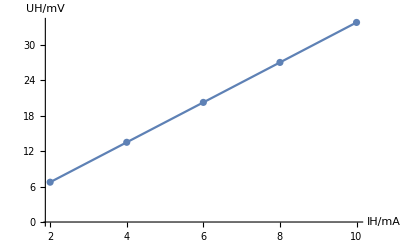

```mathematica
Show[ListPlot[Table[{data1[[1,i]],Sum[SetAccuracy[data1[[j,i]]//Abs,3],{j,6,9}]/4},{i,1,5}]],ListLinePlot[Table[{data1[[1,i]],Sum[SetAccuracy[data1[[j,i]]//Abs,3],{j,6,9}]/4},{i,1,5}]],AxesLabel->{"IH/mA","UH/mV"}]
```

```mathematica
Grid[{Prepend[Table[SetAccuracy[data2[[1,i]],4],{i,2,11}],{"IM/mA",SpanFromLeft}]//Flatten,Prepend[Table[SetAccuracy[data2[[2,i]],2],{i,2,11}],{"B/mT","B正"}]//Flatten,Prepend[Table[SetAccuracy[data2[[3,i]],2],{i,2,11}],{SpanFromAbove,"B负"}]//Flatten,Prepend[Table[Sum[SetAccuracy[data2[[j,i]],2],{j,2,3}]/2,{i,2,11}],{SpanFromAbove,"平均"}]//Flatten,Prepend[Table[SetAccuracy[data2[[4,i]],3],{i,2,11}],{"UH/mV","I正B正"}]//Flatten,Prepend[Table[SetAccuracy[data2[[5,i]],3],{i,2,11}],{SpanFromAbove,"I负B正"}]//Flatten,Prepend[Table[SetAccuracy[data2[[6,i]],3],{i,2,11}],{SpanFromAbove,"I正B负"}]//Flatten,Prepend[Table[SetAccuracy[data2[[7,i]],3],{i,2,11}],{SpanFromAbove,"I负B负"}]//Flatten,Prepend[Table[Sum[SetAccuracy[data2[[j,i]]//Abs,3],{j,4,7}]/4,{i,2,11}],{SpanFromAbove,"平均"}]//Flatten},
Frame->All,Alignment->{Center,Center},ItemSize->Full]
```

IM/mA |  | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
B/mT | B正 | 35.1 | 71. | 106.4 | 142.5 | 177.6 | 214.4 | 249.3 | 286. | 321.1 | 356.6
 | B负 | 34.9 | 70.8 | 106.3 | 141.2 | 177.2 | 212.9 | 249.3 | 284.3 | 320.7 | 354.4
 | 平均 | 35. | 70.9 | 106.4 | 141.8 | 177.4 | 213.7 | 249.3 | 285.2 | 320.9 | 355.5
UH/mV | I正B正 | -2.96 | -8.58 | -14.2 | -19.93 | -25.4 | -31.28 | -36.78 | -42.58 | -48.05 | -53.71
 | I负B正 | 2.39 | 8. | 13.63 | 19.35 | 24.83 | 30.7 | 36.21 | 42. | 47.49 | 53.14
 | I正B负 | 8.06 | 13.8 | 19.36 | 24.87 | 30.64 | 36.21 | 41.96 | 47.48 | 53.31 | 58.58
 | I负B负 | -8.63 | -14.38 | -19.93 | -25.44 | -31.2 | -36.79 | -42.55 | -48.06 | -53.87 | -59.18
 | 平均 | 5.51 | 11.19 | 16.78 | 22.4 | 28.02 | 33.75 | 39.38 | 45.03 | 50.68 | 56.15

```mathematica
LinearModelFit[Table[{Sum[data2[[j,i]]//Abs,{j,4,7}]/4,10.000*Sum[data2[[j,i]],{j,2,3}]/2/1000},{i,2,11}],x,x]
```

FittedModel[0.00099615+0.0632938 x]

```mathematica
(0.2+0.01*200)/200/Sqrt[Sum[(Sum[data2[[j,i]]//Abs,{j,4,7}]/4-Sum[Sum[data2[[j,i]]//Abs,{j,4,7}]/4,{i,2,11}]/10)^2,{i,2,11}]]
```

0.000214836

```mathematica
0.0002148362055692996/0.06329^2
```

0.0536336

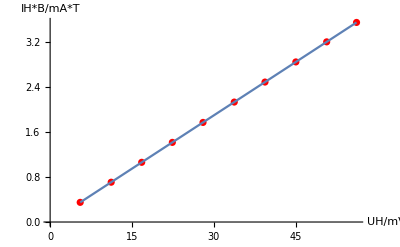

```mathematica
Show[ListPlot[Table[{1/4 ∑_(j=4)^7 Abs[data2⟦j,i⟧],(10. ∑_(j=2)^3 data2⟦j,i⟧)/(2 1000)},{i,2,11}],PlotStyle->Red],Plot[%128[x],{x,5.51,56.1525}],AxesLabel->{"UH/mV","IH*B/mA*T"}]
```

```mathematica
%62["AdjustedRSquared"]
```

1.

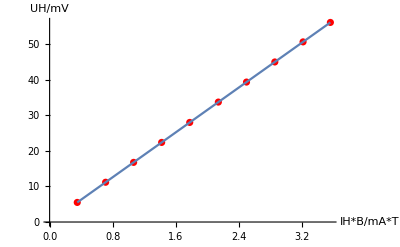

```mathematica
Show[ListPlot[Table[{(10. ∑_(j=2)^3 data2⟦j,i⟧)/(2 1000),1/4 ∑_(j=4)^7 Abs[data2⟦j,i⟧]},{i,2,11}],PlotStyle->Red],Plot[%62[x],{x,0.35000000000000003,3.5549999999999997}],AxesLabel->{"IH*B/mA*T","UH/mV"}]
```

```mathematica
Grid[{Prepend[Table[SetAccuracy[data2[[1,i]],4],{i,2,11}],{"IM/A"}]//Flatten,Prepend[Table[SetAccuracy[Sum[data2[[j,i]]//Abs,{j,4,7}]/4/(15.80*10.000)*1000,2],{i,2,11}],{"B计算/mT"}]//Flatten,Prepend[Table[Sum[SetAccuracy[data2[[j,i]],2],{j,2,3}]/2,{i,2,11}],{"B测量/mT"}]//Flatten},Frame->All,Alignment->{Center,Center},ItemSize->Full]
```

IM/A | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
B计算/mT | 34.9 | 70.8 | 106.2 | 141.8 | 177.3 | 213.6 | 249.2 | 285. | 320.8 | 355.4
B测量/mT | 35. | 70.9 | 106.4 | 141.8 | 177.4 | 213.7 | 249.3 | 285.2 | 320.9 | 355.5

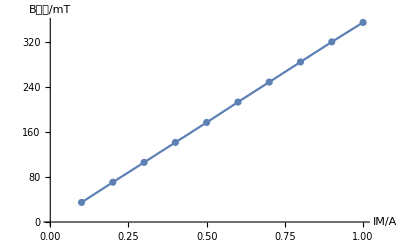

```mathematica
Show[ListPlot[Table[{data2[[1,i]],Sum[data2[[j,i]]//Abs,{j,4,7}]/4/(15.80*10.000)*1000},{i,2,11}]],ListLinePlot[Table[{data2[[1,i]],Sum[data2[[j,i]]//Abs,{j,4,7}]/4/(15.80*10.000)*1000},{i,2,11}]],AxesLabel->{"IM/A","B计算/mT"}]
```

```mathematica
Grid[{Prepend[Table[SetAccuracy[data3[[1,i]],3],{i,1,9}],"x/cm"],Prepend[Table[SetAccuracy[data3[[2,i]],3],{i,1,9}],"UH/mV"],Prepend[Table[SetAccuracy[data3[[2,i]]/(15.80*10.000)*1000,1],{i,1,9}],"B/mT"],Table[SetAccuracy[data3[[1,i]],3],{i,10,Length[data3[[1]]]}],Table[SetAccuracy[data3[[2,i]],3],{i,10,Length[data3[[2]]]}],Table[SetAccuracy[data3[[2,i]]/(15.80*10.000)*1000,1],{i,10,Length[data3[[2]]]}]}
,Frame->All,Alignment->{Center,Center},ItemSize->Full,Dividers->{{},{4->Thick}}]
```

x/cm | 5.1 | 5. | 4.9 | 4.8 | 4.7 | 4.5 | 4. | 3.5 | 3.
UH/mV | 28.44 | 32.06 | 33.05 | 32.11 | 31.79 | 31.48 | 31.33 | 31.3 | 31.28
B/mT | 180. | 203. | 209. | 203. | 201. | 199. | 198. | 198. | 198.
2.5 | 2. | 1.7 | 1.6 | 1.5 | 1.4 | 1.3 | 1.2 | 1.1 | 1.
31.28 | 31.25 | 31.13 | 31.03 | 30.85 | 30.54 | 29.9 | 28.35 | 25.5 | 21.52
198. | 198. | 197. | 196. | 195. | 193. | 189. | 179. | 161. | 136.

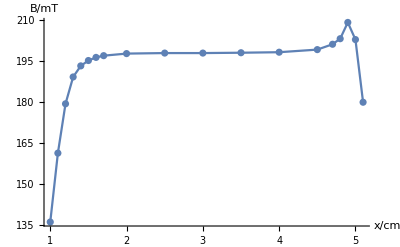

```mathematica
dotlinedraw[data_,labelx_,labely_]:=Show[ListPlot[Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}]],ListLinePlot[Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}]],AxesLabel->{labelx,labely},PlotRange->All];
data4={data3[[1]],data3[[2]]/(15.80*10.000)*1000};
dotlinedraw[data4,"x/cm","B/mT"]
```

```mathematica
σk=σyi/(√∑(xi-x平均)^2)
```

# 实验报告

系别：物理  班号：9组9号  姓名：盛凯枫  学号：1500011404  实验日期：2017年3月10日
实验名称：霍尔效应测量磁场

## 一、数据处理

### 1. 计算霍尔电压 U H ，验证 U H - I H 线性关系，并作图

#### 电流从1，2端输入，IM=0.600A

"IH/mA" |  | 2. | 4. | 6. | 8. | 10.
"UH/mV" | "I正B正" | 6.18 | 12.35 | 18.48 | 24.59 | 30.65
 | "I负B正" | -6.2 | -12.43 | -18.68 | -24.92 | -31.18
 | "I正B负" | -7.26 | -14.57 | -21.91 | -29.31 | -36.78
 | "I负B负" | 7.24 | 14.48 | 21.72 | 28.98 | 36.25
 | "平均" | 6.72 | 13.46 | 20.2 | 26.95 | 33.71

#### 电流从3，4端输入，IM=0.600A

"IH/mA" |  | 2. | 4. | 6. | 8. | 10.
"UH/mV" | "I正B正" | -7.28 | -14.58 | -21.89 | -29.21 | -36.57
 | "I负B正" | 7.28 | 14.57 | 21.88 | 29.23 | 36.6
 | "I正B负" | 6.19 | 12.39 | 18.57 | 24.76 | 30.91
 | "I负B负" | -6.18 | -12.38 | -18.57 | -24.74 | -30.91
 | "平均" | 6.73 | 13.48 | 20.23 | 26.99 | 33.75

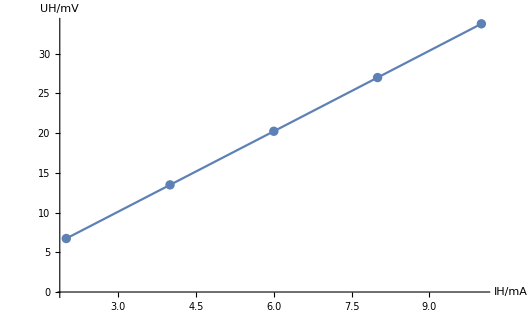

经验证电流从两种端口输入的结果没有显著区别，由图像可以得出UH与IH具有线性关系

### 2. 计算霍尔电压 U H ，验证 U H - Ｂ 线性关系；计算霍尔元件的灵敏度 K H 及其不确定度

IH=10.00mA

IM/mA |  | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
B/mT | B正 | 35.1 | 71. | 106.4 | 142.5 | 177.6 | 214.4 | 249.3 | 286. | 321.1 | 356.6
 | B负 | 34.9 | 70.8 | 106.3 | 141.2 | 177.2 | 212.9 | 249.3 | 284.3 | 320.7 | 354.4
 | 平均 | 35. | 70.9 | 106.4 | 141.8 | 177.4 | 213.7 | 249.3 | 285.2 | 320.9 | 355.5
UH/mV | I正B正 | -2.96 | -8.58 | -14.2 | -19.93 | -25.4 | -31.28 | -36.78 | -42.58 | -48.05 | -53.71
 | I负B正 | 2.39 | 8. | 13.63 | 19.35 | 24.83 | 30.7 | 36.21 | 42. | 47.49 | 53.14
 | I正B负 | 8.06 | 13.8 | 19.36 | 24.87 | 30.64 | 36.21 | 41.96 | 47.48 | 53.31 | 58.58
 | I负B负 | -8.63 | -14.38 | -19.93 | -25.44 | -31.2 | -36.79 | -42.55 | -48.06 | -53.87 | -59.18
 | 平均 | 5.51 | 11.19 | 16.78 | 22.4 | 28.02 | 33.75 | 39.38 | 45.03 | 50.68 | 56.15

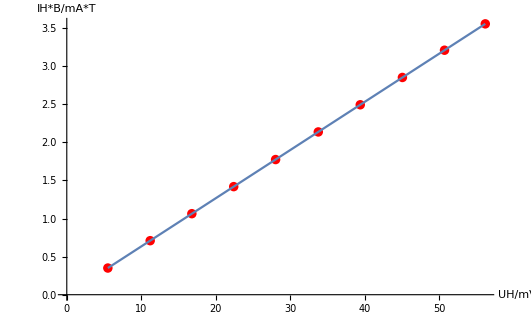
-Graphics-
由图像可知UH与B满足线性关系
拟合结果：直线方程y=0.0009962+0.06329 x，KH=1/0.06329=15.80 mV/mA*T
σKH=1/a1^2(σyi/(√∑(xi-x平均)^2)+√(1/r^2-1)/(n-2))，由于r极接近1，第二项可以忽略，σyi = 1%*B+0.2 mT ≈ 2.2mT
σKH=1/a1^2 σyi/(√∑(xi-x平均)^2)=0.05 mV/mA*T，KH=15.80±0.05 mV/mA*T

### 3. 根据２中计算的 U H 和 K H ，计算 Ｂ ，作出磁化曲线图

"IM/A" | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1.
"B计算/mT" | 34.9 | 70.8 | 106.2 | 141.8 | 177.3 | 213.6 | 249.2 | 285. | 320.8 | 355.4
"B测量/mT" | 35. | 70.9 | 106.4 | 141.8 | 177.4 | 213.7 | 249.3 | 285.2 | 320.9 | 355.5

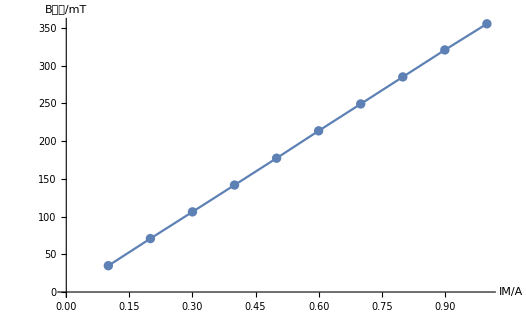

### 4. 根据测得的 U H -ｘ关系和 K H ，计算 Ｂ -ｘ关系，并作图

"x/cm" | 5.1 | 5. | 4.9 | 4.8 | 4.7 | 4.5 | 4. | 3.5 | 3.
"UH/mV" | 28.44 | 32.06 | 33.05 | 32.11 | 31.79 | 31.48 | 31.33 | 31.3 | 31.28
"B/mT" | 180. | 203. | 209. | 203. | 201. | 199. | 198. | 198. | 198.
2.5 | 2. | 1.7 | 1.6 | 1.5 | 1.4 | 1.3 | 1.2 | 1.1 | 1.
31.28 | 31.25 | 31.13 | 31.03 | 30.85 | 30.54 | 29.9 | 28.35 | 25.5 | 21.52
198. | 198. | 197. | 196. | 195. | 193. | 189. | 179. | 161. | 136.

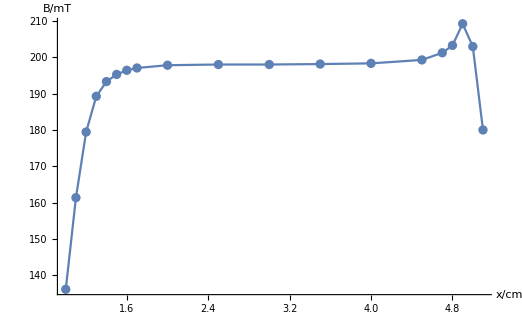

## 二、思考题

IM=0时UH仍有较小的测量值可能是因为电磁铁未完全去磁化，即仍有少量磁场残留，导致了霍尔电压的产生；另外也有可能是因为地磁场作用于霍尔片而产生的UH。

## 三、分析与讨论

### 1. 比较实验内容 1 中ａ、ｂ接法的结果，并解释现象

两种接法的结果没有显著区别，因为UH=B*IH*KH，B与IH相同，而KH只与材料性质有关而跟接法无关，所以最终得到的UH几乎相同。

### 2. 说明实验内容 3 中为什么用计算的Ｂ作磁化曲线比用直接测量的Ｂ更好

因为直接测量的B为手持特斯拉计测量得出，测量时测量端头是否垂直磁场方向有较大的不确定性，测量结果具有较大的随机误差，而使用计算得到的B则可减小随机误差。

### 3. 实验中测得的各种曲线有什么主要特征？如何理解？

实验1、2测得的曲线为直线，说明霍尔电压正比于电流和磁感应强度；实验3测得的曲线为直线，说明电磁铁产生的磁感应强度与励磁电流成正比；实验4测得的曲线在两端很低，中央几乎水平，在一侧的过渡区存在极大值的尖峰，可以理解为线圈产生的磁场在线圈内部几乎均匀，从线圈边缘向远处磁感应强度快速下降，而在边缘处由于铁芯的存在而产生了局部磁场场强的扭曲。